```mathematica
PolyhedronData["TruncatedIcosahedron"]
```

-Graphics3D-

```mathematica
PolyhedronData["TruncatedIcosahedron","EdgeCount"]
```

90

```mathematica
PolyhedronData["TruncatedIcosahedron","AdjacentFaceIndices"]
```

{{1,13},{1,14},{1,15},{1,16},{1,17},{2,13},{2,14},{2,23},{2,31},{2,32},{3,14},{3,15},{3,23},{3,24},{3,25},{4,15},{4,16},{4,25},{4,26},{4,27},{5,16},{5,17},{5,27},{5,28},{5,29},{6,13},{6,17},{6,29},{6,30},{6,31},{7,21},{7,22},{7,23},{7,24},{7,32},{8,20},{8,21},{8,24},{8,25},{8,26},{9,19},{9,20},{9,26},{9,27},{9,28},{10,18},{10,19},{10,28},{10,29},{10,30},{11,18},{11,22},{11,30},{11,31},{11,32},{12,18},{12,19},{12,20},{12,21},{12,22},{13,14},{13,17},{13,31},{14,15},{14,23},{15,16},{15,25},{16,17},{16,27},{17,29},{18,19},{18,22},{18,30},{19,20},{19,28},{20,21},{20,26},{21,22},{21,24},{22,32},{23,24},{23,32},{24,25},{25,26},{26,27},{27,28},{28,29},{29,30},{30,31},{31,32}}

```mathematica
"显示带有指标顶点的多面体"%12Show[PolyhedronData["TruncatedIcosahedron"],Graphics3D[MapThread[Text,{PolyhedronData["TruncatedIcosahedron","VertexIndices"],1.05 PolyhedronData["TruncatedIcosahedron","VertexCoordinates"]}]]]
```

-Graphics3D-

```mathematica
Graph3D[Flatten@{0<->1,0<->2,0<->3,0<->4,0<->5,1<->2,2<->3,3<->4,4<->5,5<->1,6<->1,6<->5,7<->1,7<->2,8<->2,8<->3,9<->3,9<->4,10<->4,10<->5,6<->7,7<->8,8<->9,9<->10,10<->6,Table[11<->i,{i,6,10}]},VertexLabels->"Name"]
```

-Graphics3D-

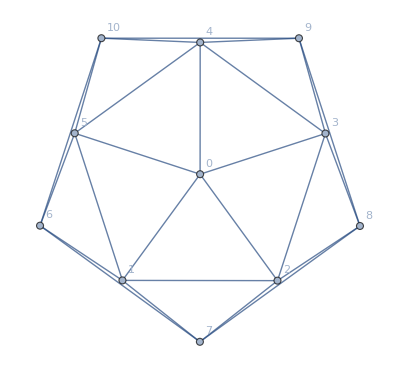

```mathematica
Graph[Flatten@{0<->1,0<->2,0<->3,0<->4,0<->5,1<->2,2<->3,3<->4,4<->5,5<->1,6<->1,6<->5,7<->1,7<->2,8<->2,8<->3,9<->3,9<->4,10<->4,10<->5,6<->7,7<->8,8<->9,9<->10,10<->6},VertexLabels->"Name"]
```

```mathematica
neighbors={{25,1,4},{5,0,2},{10,1,3},{15,2,4},{20,3,0},{1,6,9},{29,5,7},{31,6,8},{38,7,9},{11,8,5},{2,11,14},{9,10,12},{37,11,13},{41,12,14},{16,13,10},{3,16,19},{14,15,17},{40,16,18},{46,17,19},{21,18,15},{4,21,24},{19,20,22},{45,21,23},{51,22,24},{26,23,20},{0,26,29},{24,25,27},{50,26,28},{32,27,29},{6,28,25},{39,31,34},{7,30,32},{28,31,33},{54,32,34},{55,33,30},{56,36,39},{42,35,37},{12,36,38},{8,37,39},{30,38,35},{17,41,44},{13,40,42},{36,41,43},{57,42,44},{47,43,40},{22,46,49},{18,45,47},{44,46,48},{58,47,49},{52,48,45},{27,51,54},{23,50,52},{49,51,53},{59,52,54},{33,53,50},{34,56,59},{35,55,57},{43,56,58},{48,57,59},{53,58,55}}+1;
ground={1,-1, 1,-1, 1, 1,-1, 1, 1,-1,-1,-1, 1,-1, 1, 1,-1, 1, 1, 1,-1,-1, 1,-1, 1,-1, 1, 1, 1, 1,-1,-1,-1, 1,-1,-1, 1,-1,-1, 1,-1, 1,-1,-1, 1,-1, 1,-1, 1, 1,-1, 1, 1,-1, 1, 1,-1, 1,-1, 1};
color=ground/.{-1->Blue,1->Red};
Graph3D[Union@Flatten@Table[Sort[i<->neighbors[[i,j]]],{i,1,60},{j,1,3}],VertexLabels->"Name",VertexStyle->Table[i->color[[i]],{i,1,60}],VertexSize->0.5]
```

-Graphics3D-